## Useful Information

units
mV
pA
nS
pF

key functions and parameters

actInfX[v]		steady-state activation for conductance X (for single gating variable)
inactInfX[v]		steady-state inactivation for conductance X
actTauX[v]		activation time constant for conductance X
inactTauX[v]		inactivation time constant for conductance X

vHaX			half activation voltage for conductance X
vSaX			activation slope factor for conductance X
vHiX			half inactivation voltage for conductance X
vSiX			inactivation slope factor for conductance X

t1X			minimum gating time constant of conductance X
t2X			scale parameter for gating time constant of conductance X
vH1X			location paramerer for voltage dependence of time constant (falling phase, if vS1X > 0)
vS1X			slope factor for voltage dependence of time constant (falling phase, if  > 0)
vH2X			location paramerer for voltage dependence of time constant (rising phase, if vS2X < 0)
vS2X			slope factor for voltage dependence of time constant (rising phase, if < 0)

Distinguish activation from inactivation with “a” or “i” if necessary
Example: t2aX = scale parameter for activation time constant of conductance X. 

tempX			temperature at which X’s time constant is specified by the above parameters
Q10aX			Q10 for conductance X activation kinetics
Q10iX			Q10 for conductance X inactivation kinetics
Q10gX			Q10 for total conductance of type X

mX			activation gating variable for conductance X
hX			inactivation gating variable for conductance X
gMaxX			maximal X conductance
nX			activation cooperativity for conductance X (conductance X  = mX^nX gMaxX)

conductance abbreviations (“X”)

Na			spiking (inactivating) Na
Kdr			K delayed rectifier
A			rapidly inactivating K
D			slowly inactivating K
K2			very slowly inactivating K
H			hyperpolarization-activated cation (HCN)
T			inactivating, low threshold Ca

## Define Basic Procedures

```mathematica
SetOptions[ListPlot,PlotRange->All,Joined->True,PlotStyle->Thickness[0.005]];
SetOptions[Plot,PlotRange->All,PlotStyle->Thickness[0.005]];
```

```mathematica
FindSpikes[vTraj_,startV_:0,endV_:-5]:=Module[{spike,spkTimes,remainder,startLoc,spkLoc},

spike=False;
spkTimes={};
Do[
If[vTraj[[i,2]]>startV&&!spike,spike=True;startLoc=i];
If[vTraj[[i,2]]<endV&&spike,
spike=False;
spkLoc=Position[vTraj[[startLoc;;i,2]],Max[vTraj[[startLoc;;i,2]]]][[1,1]];
AppendTo[spkTimes,vTraj[[startLoc;;i,1]][[spkLoc]]]
],
{i,Length[vTraj]}];

If[spike,
remainder=Most[vTraj[[startLoc;;]]],
remainder={}
];

Return[{spkTimes,remainder}]
];
```

```mathematica
SaturateDeriv[x_,linearMax_,absoluteMax_]:= Piecewise[{{1,x≤linearMax },{Sech[(x-linearMax)/(absoluteMax-linearMax)]^2,x>linearMax }}]
```

## Define Basic Gating Functions

```mathematica
xInf[v_,vH_,vS_]:=1/(1+Exp[(v-vH)/vS])
```

```mathematica
xTau[v_,t1_,t2_,vH1_,vS1_,vH2_,vS2_]:=t1+t2/((1+Exp[(v-vH1)/vS1])(1+Exp[(v-vH2)/vS2]))
```

```mathematica
xDot[x_,xInf_,tau_]:=(xInf-x)/tau
```

## Define Voltage-Dependent Conductances

TempAdjust returns a factor that can be used to adjust model parameters (time constants or conductances) to the values they should adopt at different temperatures.  A parameter is adjusted by multiplying it by the factor returned by TempAdjust

```mathematica
TempAdjust[tempBase_,tempTarget_,Q10_:3]:=Q10^((tempBase-tempTarget)/10)
```

```mathematica
tempZF=41; (* zebra finch body temperature *)
tempRoom=25; (* presumed temperature during unheated slice recordings *)
```

### Spiking Na (instantaneous activation) -- Na

#### steady-state activation

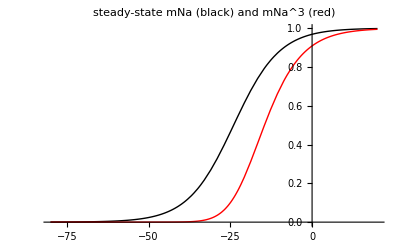

```mathematica
vHaNa=-24; (* half activation voltage *)
vSaNa=-7;   (* activation slope factor *)
nNa=3;              (* activation variable exponent *)

actInfNa[v_]:=xInf[v,vHaNa,vSaNa];
labelStr="steady-state mNa (black) and mNa^"<>ToString[nNa]<>" (red)";
Plot[{actInfNa[v],actInfNa[v]^nNa},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Black,Red},PlotLabel->labelStr]
```

#### steady-state inactivation

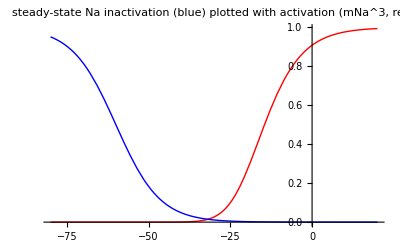

```mathematica
vHiNa=-60; (* half inactivation voltage *)
vSiNa=6.7;   (* inactivation slope factor *)

inactInfNa[v_]:=xInf[v,vHiNa,vSiNa];
labelStr="steady-state Na inactivation (blue)\nplotted with activation (mNa^"<>ToString[nNa]<>", red)";
Plot[{actInfNa[v]^nNa,inactInfNa[v]},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Red,Blue},PlotLabel->labelStr]
```

#### inactivation time constant

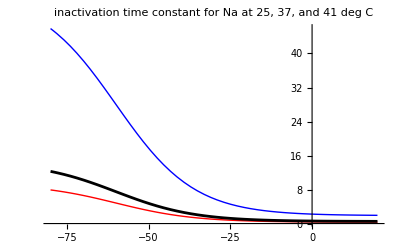

```mathematica
t1iNa=0.5;
t2iNa=14;
vH1iNa=-120;
vS1iNa=-5;
vH2iNa=-60;
vS2iNa=12;

tempNa=37; (* presumed temperature at which these kinetics apply *)
Q10iNa=3;

qRoom=TempAdjust[tempNa,tempRoom,Q10iNa];
qZF=TempAdjust[tempNa,tempZF,Q10iNa];
labelStr="inactivation time constant for Na at "<>ToString[tempRoom]<>", "<>ToString[tempNa]<>", and "<>ToString[tempZF]<>" deg C";
inactTauNa[v_]:=xTau[v,t1iNa,t2iNa,vH1iNa,vS1iNa,vH2iNa,vS2iNa]
Plot[{qRoom inactTauNa[v],qZF inactTauNa[v],inactTauNa[v]},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

### Kv3.1/3.2 (delayed rectifier) -- Kdr

#### steady-state activation

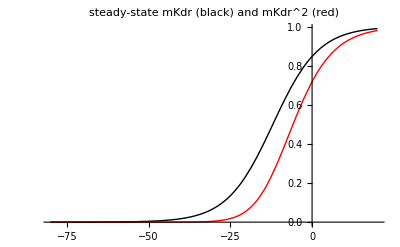

```mathematica
vHaKdr=-12; (* half activation voltage *)
vSaKdr=-7;   (* activation slope factor *)
nKdr=2;              (* activation variable exponent *)

actInfKdr[v_]:=xInf[v,vHaKdr,vSaKdr];
labelStr="steady-state mKdr (black) and mKdr^"<>ToString[nKdr]<>" (red)";
Plot[{actInfKdr[v],actInfKdr[v]^nKdr},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Black,Red},PlotLabel->labelStr]
```

#### activation time constant

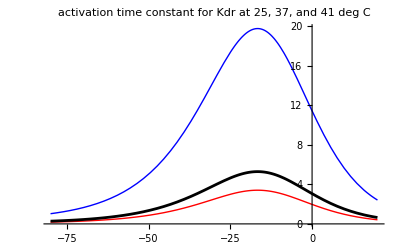

```mathematica
t1aKdr=0.1;
t2aKdr=40;
vH1aKdr=-14.6;
vS1aKdr=8.6;
vH2aKdr=1.3;
vS2aKdr=-15;

tempKdr=37; (* presumed temperature at which these kinetics apply *)
Q10aKdr=3; 

qRoom=TempAdjust[tempKdr,tempRoom,Q10aKdr];
qZF=TempAdjust[tempKdr,tempZF,Q10aKdr];
labelStr="activation time constant for Kdr at "<>ToString[tempRoom]<>", "<>ToString[tempKdr]<>", and "<>ToString[tempZF]<>" deg C";
actTauKdr[v_]:=xTau[v,t1aKdr,t2aKdr,vH1aKdr,vS1aKdr,vH2aKdr,vS2aKdr];
Plot[{qRoom actTauKdr[v],qZF actTauKdr[v],actTauKdr[v]},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

### Kv4 (rapidly inactivating K current) -- A

#### steady-state activation

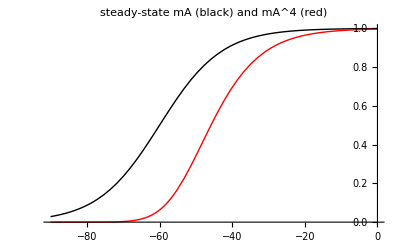

```mathematica
vHaA=-60; (* half activation voltage *)
vSaA=-8.5;   (* activation slope factor *)
nA=4;              (* activation variable exponent *)

actInfA[v_]:=xInf[v,vHaA,vSaA];
labelStr="steady-state mA (black) and mA^"<>ToString[nA]<>" (red)";
Plot[{actInfA[v],actInfA[v]^nA},{v,-90,0},AxesOrigin->{0,0},PlotStyle->{Black,Red},PlotLabel->labelStr]
```

#### steady-state inactivation

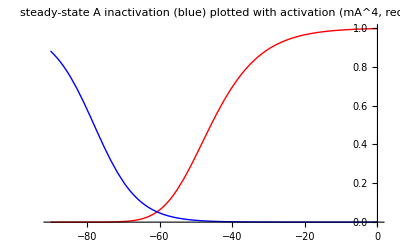

```mathematica
vHiA=-78; (* half inactivation voltage *)
vSiA=6;   (* inactivation slope factor *)

inactInfA[v_]:=xInf[v,vHiA,vSiA];
labelStr="steady-state A inactivation (blue)\nplotted with activation (mA^"<>ToString[nA]<>", red)";
Plot[{actInfA[v]^nA,inactInfA[v]},{v,-90,0},AxesOrigin->{0,0},PlotStyle->{Red,Blue},PlotLabel->labelStr]
```

#### activation time constant

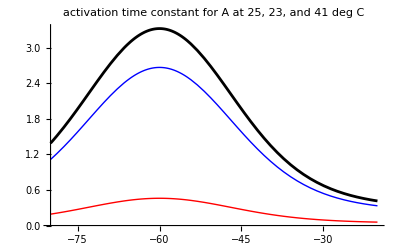

```mathematica
t1aA=0.3;
t2aA=5;
vH1aA=-50;
vS1aA=8;
vH2aA=-70;
vS2aA=-8;

tempA=23; (* presumed temperature at which these kinetics apply *)
Q10aA=3; 

qRoom=TempAdjust[tempA,tempRoom,Q10aA];
qZF=TempAdjust[tempA,tempZF,Q10aA];
labelStr="activation time constant for A at "<>ToString[tempRoom]<>", "<>ToString[tempA]<>", and "<>ToString[tempZF]<>" deg C";
actTauA[v_]:=xTau[v,t1aA,t2aA,vH1aA,vS1aA,vH2aA,vS2aA];
Plot[{qRoom actTauA[v],qZF actTauA[v],actTauA[v]},{v,-80,-20},AxesOrigin->{-80,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

#### inactivation time constant (fixed, voltage-independent)

```mathematica
inactTauA[v_]:=20;

Q10iA=3;

qRoom=TempAdjust[tempA,tempRoom,Q10iA];
qZF=TempAdjust[tempA,tempZF,Q10iA];
Print["A current inactivation time constant at ",tempRoom," and ",tempZF," deg C: ",N[qRoom inactTauA[0]]," ms, ",N[qZF inactTauA[0]]," ms"]
```

A current inactivation time constant at 25 and 41 deg C: 16.0548 ms, 2.76829 ms

### Kv1 (slowly inactivating K current) -- D

#### steady-state activation

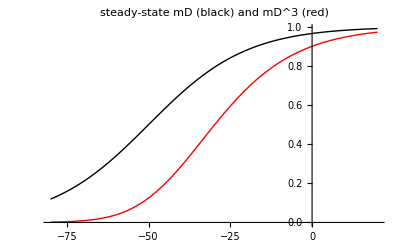

```mathematica
vHaD=-50; (* half activation voltage *)
vSaD=-15;   (* activation slope factor *)
nD=3;              (* activation variable exponent *)

actInfD[v_]:=xInf[v,vHaD,vSaD];
labelStr="steady-state mD (black) and mD^"<>ToString[nD]<>" (red)";
Plot[{actInfD[v],actInfD[v]^nD},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Black,Red},PlotLabel->labelStr]
```

#### steady-state inactivation

```mathematica
vHiD=-70; (* half inactivation voltage *)
vSiD=6;   (* inactivation slope factor *)
```

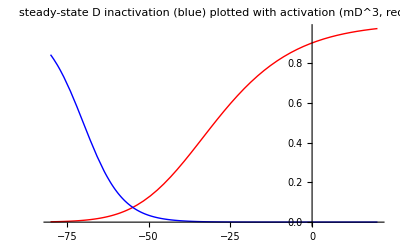

```mathematica
inactInfD[v_]:=xInf[v,vHiD,vSiD];
labelStr="steady-state D inactivation (blue)\nplotted with activation (mD^"<>ToString[nD]<>", red)";
Plot[{actInfD[v]^nD,inactInfD[v]},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Red,Blue},PlotLabel->labelStr]
```

#### activation time constant

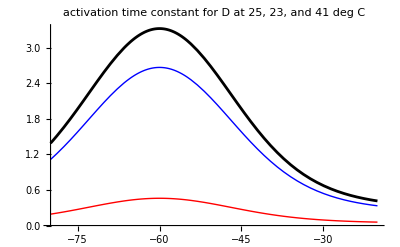

```mathematica
t1aD=0.3;
t2aD=5;
vH1aD=-50;
vS1aD=8;
vH2aD=-70;
vS2aD=-8;

tempD=23; (* presumed temperature at which these kinetics apply *)
Q10aD=3; 

qRoom=TempAdjust[tempD,tempRoom,Q10aD];
qZF=TempAdjust[tempD,tempZF,Q10aD];
labelStr="activation time constant for D at "<>ToString[tempRoom]<>", "<>ToString[tempD]<>", and "<>ToString[tempZF]<>" deg C";
actTauD[v_]:=xTau[v,t1aD,t2aD,vH1aD,vS1aD,vH2aD,vS2aD];
Plot[{qRoom actTauD[v],qZF actTauD[v],actTauD[v]},{v,-80,-20},AxesOrigin->{-80,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

#### inactivation time constant (fixed, voltage-independent)

```mathematica
inactTauD[v_]:=100;
 
Q10iD=3;

qRoom=TempAdjust[tempD,tempRoom,Q10iD];
qZF=TempAdjust[tempD,tempZF,Q10iD];
Print["D current inactivation time constant at ",tempRoom," and ",tempZF," deg C: ",N[qRoom inactTauD[0]]," ms, ",N[qZF inactTauD[0]]," ms"]
```

D current inactivation time constant at 25 and 41 deg C: 80.2742 ms, 13.8415 ms

### Kv? ( very slowly inactivating K current) -- K2

#### steady-state activation

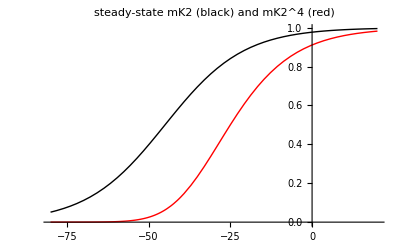

```mathematica
vHaK2=-45; (* half activation voltage *)
vSaK2=-12;   (* activation slope factor *)
nK2=4;              (* activation variable exponent *)

actInfK2[v_]:=xInf[v,vHaK2,vSaK2];
labelStr="steady-state mK2 (black) and mK2^"<>ToString[nK2]<>" (red)";
Plot[{actInfK2[v],actInfK2[v]^nK2},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Black,Red},PlotLabel->labelStr]
```

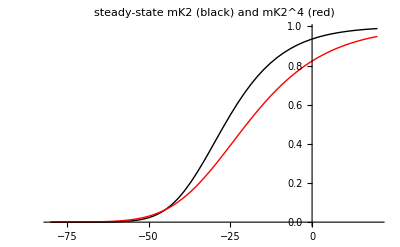

```mathematica
Plot[{xInf[v,vHaK2,-11]^nK2,xInf[v,vHaK2,-15]^nK2},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Black,Red},PlotLabel->labelStr]
```

#### steady-state inactivation

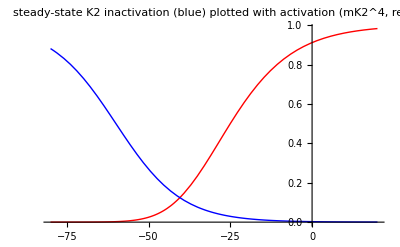

```mathematica
vHiK2=-60; (* half inactivation voltage *)
vSiK2=10;   (* inactivation slope factor *)

inactInfK2[v_]:=xInf[v,vHiK2,vSiK2];
labelStr="steady-state K2 inactivation (blue)\nplotted with activation (mK2^"<>ToString[nK2]<>", red)";
Plot[{actInfK2[v]^nK2,inactInfK2[v]},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Red,Blue},PlotLabel->labelStr]
```

#### activation time constant

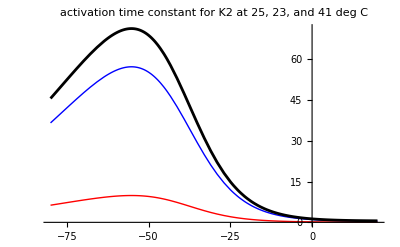

```mathematica
t1aK2=0.5;
t2aK2=120;
vH1aK2=-40;
vS1aK2=8;
vH2aK2=-70;
vS2aK2=-20;

tempK2=23; (* presumed temperature at which these kinetics apply *)
Q10aK2=3; 

qRoom=TempAdjust[tempK2,tempRoom,Q10aK2];
qZF=TempAdjust[tempK2,tempZF,Q10aK2];
labelStr="activation time constant for K2 at "<>ToString[tempRoom]<>", "<>ToString[tempK2]<>", and "<>ToString[tempZF]<>" deg C";
actTauK2[v_]:=xTau[v,t1aK2,t2aK2,vH1aK2,vS1aK2,vH2aK2,vS2aK2];
Plot[{qRoom actTauK2[v],qZF actTauK2[v],actTauK2[v]},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

#### inactivation time constant (fixed, voltage-independent)

```mathematica
inactTauK2[v_]:=8000;
 
Q10iK2=3;

qRoom=TempAdjust[tempK2,tempRoom,Q10iK2];
qZF=TempAdjust[tempK2,tempZF,Q10iK2];
Print["K2 current inactivation time constant at ",tempRoom," and ",tempZF," deg C: ",N[qRoom inactTauK2[0]]," ms, ",N[qZF inactTauK2[0]]," ms"]
```

K2 current inactivation time constant at 25 and 41 deg C: 6421.93 ms, 1107.32 ms

### HCN -- H

#### steady-state activation

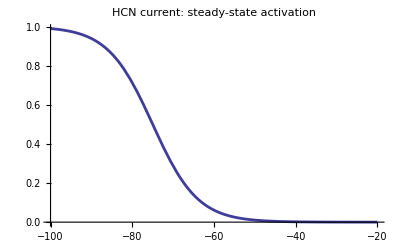

```mathematica
vHaH=-75;   (* half activation voltage *)
vSaH=5.5; (* activation slope factor *)

actInfH[v_]:=xInf[v,vHaH,vSaH]
labelStr="HCN current: steady-state activation";
Plot[actInfH[v],{v,-100,-20},PlotRange->{0,All},PlotLabel->labelStr]
```

#### activation time constant

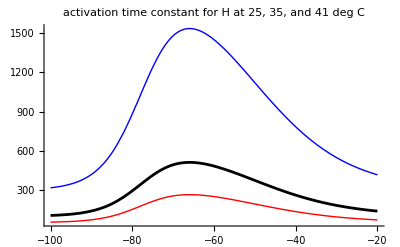

```mathematica
(* based on Huguenard and McCormick 1992 *)
t1aH=100;
t2aH=600;
vH1aH=-77;
vS1aH=-5;
vH2aH=-52;
vS2aH=12;

tempH=35; (* presumed temperature at which these kinetics apply *)
Q10aH=3; 

qRoom=TempAdjust[tempH,tempRoom,Q10aH];
qZF=TempAdjust[tempH,tempZF,Q10aH];
labelStr="activation time constant for H at "<>ToString[tempRoom]<>", "<>ToString[tempH]<>", and "<>ToString[tempZF]<>" deg C";
actTauH[v_]:=xTau[v,t1aH,t2aH,vH1aH,vS1aH,vH2aH,vS2aH];
Plot[{qRoom actTauH[v],qZF actTauH[v],actTauH[v]},{v,-100,-20},AxesOrigin->{-100,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

### T-type Calcium -- T

#### steady-state activation

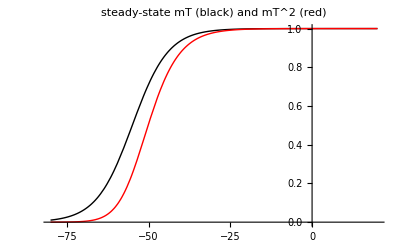

```mathematica
vHaT=-55;   (* half activation voltage *)
vSaT=-5.5; (* activation slope factor *)
nT=2;(* activation variable exponent *)

actInfT[v_]:=xInf[v,vHaT,vSaT];
labelStr="steady-state mT (black) and mT^"<>ToString[nT]<>" (red)";
Plot[{actInfT[v],actInfT[v]^nT},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Black,Red},PlotLabel->labelStr]
```

#### steady-state inactivation

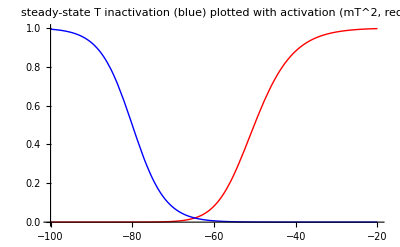

```mathematica
vHiT=-80;   (* half inactivation voltage *)
vSiT=4;      (* inactivation slope factor *)

inactInfT[v_]:=xInf[v,vHiT,vSiT];
labelStr="steady-state T inactivation (blue)\nplotted with activation (mT^"<>ToString[nT]<>", red)";
Plot[{actInfT[v]^nT,inactInfT[v]},{v,-100,-20},AxesOrigin->{-100,0},PlotStyle->{Red,Blue},PlotLabel->labelStr]
```

#### activation time constant

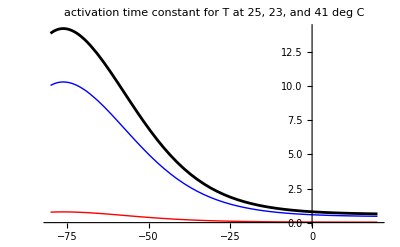

```mathematica
(* based on Huguenard and McCormick 1992 *)
t1aT=0.6;
t2aT=20;
vH1aT=-90;
vS1aT=-7;
vH2aT=-60;
vS2aT=13;

tempT=23; (* presumed temperature at which these kinetics apply *)
Q10aT=5; 

qRoom=TempAdjust[tempT,tempRoom,Q10aT];
qZF=TempAdjust[tempT,tempZF,Q10aT];
labelStr="activation time constant for T at "<>ToString[tempRoom]<>", "<>ToString[tempT]<>", and "<>ToString[tempZF]<>" deg C";
actTauT[v_]:=xTau[v,t1aT,t2aT,vH1aT,vS1aT,vH2aT,vS2aT];
Plot[{qRoom actTauT[v],qZF actTauT[v],actTauT[v]},{v,-80,20},AxesOrigin->{0,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

#### inactivation time constant

```mathematica
vH1=-97;
vS1=-12;
vH2=-77;
vS2=6;
t1=30;
t2=380;
```

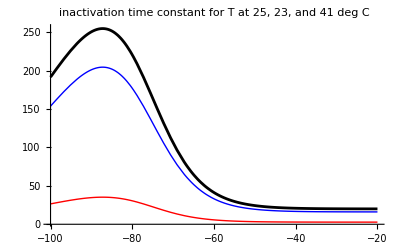

```mathematica
(* roughly based Destexhe et al. 1996 *)
t1iT=20;
t2iT=400;
vH1iT=-97;
vS1iT=-12;
vH2iT=-77;
vS2iT=6;

Q10iT=3;

qRoom=TempAdjust[tempT,tempRoom,Q10iT];
qZF=TempAdjust[tempT,tempZF,Q10iT];
labelStr="inactivation time constant for T at "<>ToString[tempRoom]<>", "<>ToString[tempT]<>", and "<>ToString[tempZF]<>" deg C";
inactTauT[v_]:=xTau[v,t1iT,t2iT,vH1iT,vS1iT,vH2iT,vS2iT]
Plot[{qRoom inactTauT[v],qZF inactTauT[v],inactTauT[v]},{v,-100,-20},AxesOrigin->{-100,0},PlotStyle->{Blue,Red,Directive[Black,Thickness[0.005]]},PlotLabel->labelStr]
```

## Set Other Model Parameters and Define IPSC

### Set Parameters, Define Membrane Current Equations

NOTE: mS/cm^2 * pF = nS

```mathematica
(* conductance parameters, nS *)
gLeak=1.5;
gMaxNa=5000;
gMaxKdr=500;
gMaxA=4;
gMaxD=4;
gMaxK2=10;
gMaxH=6.5;
gMaxT=30;
```

```mathematica
(* ionic driving forces, mV *)
eNa=50;
eK=-100;
eCa=100;
eLeak=-60;
eH=-40;
eGlut=0;
eGaba=-95;
```

```mathematica
(* cell capacitance, pF *)
capacitance=50;
```

```mathematica
(* Q10 values for peak condunctances *)
Q10gNa=2;
Q10gKdr=1.5;
Q10gA=1.5;
Q10gD=1.5;
Q10gK2=1.5;
Q10gH=2.5;
Q10gT=3;
Q10gLeak=1.5;

tempBase=25;
```

```mathematica
(* temperature at which the model is supposed to run *)
temp=25;

QiNa=TempAdjust[tempNa,temp,Q10iNa];
QgNa=TempAdjust[tempNa,temp,Q10gNa]^-1;

QaKdr=TempAdjust[tempKdr,temp,Q10aKdr];
QgKdr=TempAdjust[tempBase,temp,Q10gKdr]^-1;

QaA=TempAdjust[tempA,temp,Q10aA];
QiA=TempAdjust[tempA,temp,Q10iA];
QgA=TempAdjust[tempBase,temp,Q10gA]^-1;

QaD=TempAdjust[tempD,temp,Q10aD];
QiD=TempAdjust[tempD,temp,Q10iD];
QgD=TempAdjust[tempBase,temp,Q10gD]^-1;

QaK2=TempAdjust[tempK2,temp,Q10aK2];
QiK2=TempAdjust[tempK2,temp,Q10iK2];
QgK2=TempAdjust[tempBase,temp,Q10gK2]^-1;

QaH=TempAdjust[tempH,temp,Q10aH];
QgH=TempAdjust[tempBase,temp,Q10gH]^-1;

QaT=TempAdjust[tempT,temp,Q10aT];
QiT=TempAdjust[tempT,temp,Q10iT];
QgT=TempAdjust[tempBase,temp,Q10gT]^-1;

QgLeak=TempAdjust[tempBase,temp,Q10gLeak]^-1;
```

```mathematica
(* membrane current equations *)

iNa[v_,hNa_]:=actInfNa[v]^nNa hNa QgNa gMaxNa(v-eNa);

iK[v_,mKdr_,mA_,hA_,mD_,hD_,mK2_,hK2_]:=(mA^nA hA QgA gMaxA+mD^nD hD QgD gMaxD+mK2^nK2 hK2 QgK2 gMaxK2+mKdr^nKdr QgKdr gMaxKdr)(v-eK);

iH[v_,mH_]:=mH QgH gMaxH(v-eH);

iCa[v_,mT_,hT_]:=mT^nT hT QgT gMaxT(v-eCa);

vDot[v_,iInj_,gGlut_,gGaba_,hNa_,mKdr_,mA_,hA_,mD_,hD_,mK2_,hK2_,mH_,mT_,hT_]:=(iInj-iNa[v,hNa]-iK[v,mKdr,mA,hA,mD,hD,mK2,hK2]-iH[v,mH]-iCa[v,mT,hT]-gGlut(v-eGlut)-gGaba(v-eGaba)-QgLeak gLeak(v-eLeak))/capacitance;
```

### Define IPSC

```mathematica
tauRiseBase=0.7;
tauDecayBase=10;
gGabaBase=12;                             (* peak unitary IPSC conductance *)
gMaxGabaBase=gGabaBase+3;  (* maximum possible GABA conductance *)
tempGaba=25;
Q10rGaba=2.1; (* Q10 for GABA rise kinetics *)
Q10dGaba=2.1; (* Q10 for GABA decay kinetics *)
Q10gGaba=1.5; (* Q10 for GABA conductance *)

tauRise=TempAdjust[tempGaba,temp,Q10rGaba] tauRiseBase;
tauDecay=TempAdjust[tempGaba,temp,Q10dGaba] tauDecayBase;
gUnitaryGaba=gGabaBase/TempAdjust[tempGaba,temp,Q10gGaba];
gMaxGaba=gMaxGabaBase/TempAdjust[tempGaba,temp,Q10gGaba];
gabaPeakTime=(Log[1/tauDecay]-Log[(tauRise+tauDecay)/(tauRise tauDecay)])/(1/tauDecay-(tauRise+tauDecay)/(tauRise tauDecay));
gabaNorm=1/((1-Exp[-gabaPeakTime/tauRise])Exp[-gabaPeakTime/tauDecay]);
```

### Define Procedure for Changing Model Temperature

SetTemperature adjusts all model parameters to make them conform to the selected temperature.  It also computes the resting state given those adjustments.  If given a second argument True, it prints out a brief report of model properties at that temperature.

```mathematica
SetTemperature[temp_,print_:False]:=Module[{vTraj,tf,s,times,rest},

QiNa=TempAdjust[tempNa,temp,Q10iNa];
QgNa=TempAdjust[tempBase,temp,Q10gNa]^-1;

QaKdr=TempAdjust[tempKdr,temp,Q10aKdr];
QgKdr=TempAdjust[tempBase,temp,Q10gKdr]^-1;

QaA=TempAdjust[tempA,temp,Q10aA];
QiA=TempAdjust[tempA,temp,Q10iA];
QgA=TempAdjust[tempBase,temp,Q10gA]^-1;

QaD=TempAdjust[tempD,temp,Q10aD];
QiD=TempAdjust[tempD,temp,Q10iD];
QgD=TempAdjust[tempBase,temp,Q10gD]^-1;

QaK2=TempAdjust[tempK2,temp,Q10aK2];
QiK2=TempAdjust[tempK2,temp,Q10iK2];
QgK2=TempAdjust[tempBase,temp,Q10gK2]^-1;

QaH=TempAdjust[tempH,temp,Q10aH];
QgH=TempAdjust[tempBase,temp,Q10gH]^-1;

QaT=TempAdjust[tempT,temp,Q10aT];
QiT=TempAdjust[tempT,temp,Q10iT];
QgT=TempAdjust[tempBase,temp,Q10gT]^-1;

QgLeak=TempAdjust[tempBase,temp,Q10gLeak]^-1;

(* compute GABA PSC waveform *)
tauRise=TempAdjust[tempGaba,temp,Q10rGaba] tauRiseBase;
tauDecay=TempAdjust[tempGaba,temp,Q10dGaba] tauDecayBase;
gUnitaryGaba=gGabaBase/TempAdjust[tempGaba,temp,Q10gGaba];
gMaxGaba=gMaxGabaBase/TempAdjust[tempGaba,temp,Q10gGaba];
gabaPeakTime=(Log[1/tauDecay]-Log[(tauRise+tauDecay)/(tauRise tauDecay)])/(1/tauDecay-(tauRise+tauDecay)/(tauRise tauDecay));
gabaNorm=1/((1-Exp[-gabaPeakTime/tauRise])Exp[-gabaPeakTime/tauDecay]);
gabaPsc[t_,tStim_]:=Piecewise[{{0,t<tStim},{gabaNorm(1-Exp[-(t-tStim)/tauRise])Exp[-(t-tStim)/tauDecay],t≥tStim}}];

(* compute resting state *)
diffEq={
v'[t]==vDot[v[t],0,0,0,hNa[t],mKdr[t],mA[t],hA[t],mD[t],hD[t],mK2[t],hK2[t],mH[t],mT[t],hT[t]],
hNa'[t]==xDot[hNa[t],inactInfNa[v[t]],QiNa inactTauNa[v[t]]],
mKdr'[t]==xDot[mKdr[t],actInfKdr[v[t]],QaKdr actTauKdr[v[t]]],
mA'[t]==xDot[mA[t],actInfA[v[t]],QaA actTauA[v[t]]],
hA'[t]==xDot[hA[t],inactInfA[v[t]],QiA inactTauA[v[t]]],
mD'[t]==xDot[mD[t],actInfD[v[t]],QaD actTauD[v[t]]],
hD'[t]==xDot[hD[t],inactInfD[v[t]],QiD inactTauD[v[t]]],
mK2'[t]==xDot[mK2[t],actInfK2[v[t]],QaK2 actTauK2[v[t]]],
hK2'[t]==xDot[hK2[t],inactInfK2[v[t]],QiK2 inactTauK2[v[t]]],
mH'[t]==xDot[mH[t],actInfH[v[t]],QaH actTauH[v[t]]],
mT'[t]==xDot[mT[t],actInfT[v[t]],QaT actTauT[v[t]]],
hT'[t]==xDot[hT[t],inactInfT[v[t]],QiT inactTauT[v[t]]]
};
v0=-60;
initCond={
v[0]==v0,
hNa[0]==inactInfNa[v0],
mKdr[0]==actInfKdr[v0],
mA[0]==actInfA[v0],
hA[0]==inactInfA[v0],
mD[0]==actInfD[v0],
hD[0]==inactInfD[v0],
mK2[0]==actInfK2[v0],
hK2[0]==inactInfK2[v0],
mH[0]==actInfH[v0],
mT[0]==actInfT[v0],
hT[0]==inactInfT[v0]
};
eqn=Join[diffEq,initCond];
tf=50000;
s=NDSolve[eqn,{v,hNa,mKdr,mA,hA,mD,hD,mK2,hK2,mH,mT,hT},{t,0,tf},MaxSteps->Infinity];
v0=Evaluate[v[tf]/.s][[1]];
hNa0=Evaluate[hNa[tf]/.s][[1]];
mKdr0=Evaluate[mKdr[tf]/.s][[1]];
mD0=Evaluate[mD[tf]/.s][[1]];
hD0=Evaluate[hD[tf]/.s][[1]];
mA0=Evaluate[mA[tf]/.s][[1]];
hA0=Evaluate[hA[tf]/.s][[1]];
mK20=Evaluate[mK2[tf]/.s][[1]];
hK20=Evaluate[hK2[tf]/.s][[1]];
mH0=Evaluate[mH[tf]/.s][[1]];
mT0=Evaluate[mT[tf]/.s][[1]];
hT0=Evaluate[hT[tf]/.s][[1]];
initCond={
v[0]==v0,
hNa[0]==hNa0,
mKdr[0]==mKdr0,
mD[0]==mD0,
hD[0]==hD0,
mA[0]==mA0,
hA[0]==hA0,
mK2[0]==mK20,
hK2[0]==hK20,
mH[0]==mH0,
mT[0]==mT0,
hT[0]==hT0
};
times=Table[t,{t,tf-1000,tf,0.1}];
vTraj=Transpose[{times,Evaluate[v[#]/.s][[1]]&/@times}];
If[Length[FindSpikes[vTraj][[1]]]==0,
rest="resting potential: "<>ToString[Round[v0,0.1]]<>" mV",
rest="Model is autonomously active!";
Print[rest]
];

If[print,
Print[rest];
Print["IPSC properties at ",temp," deg:\n",Round[tauRise,0.1]," ms rise tau, ",Round[tauDecay,0.1]," ms decay tau\n",Round[gUnitaryGaba,0.1]," nS peak unitary conductance"]
]
]
```

## DLM at 25°C

```mathematica
SetTemperature[25,True]
```

resting potential: -57.2 mV

IPSC properties at 25 deg:
0.7 ms rise tau, 10. ms decay tau
12. nS peak unitary conductance

### Series of Current Pulses

#### Specify Current Injection

```mathematica
dcLevel=0; (* pA *)
tStep=500;
tDur=2000;
tPost=1000;
pulseSize=Table[i,{i,50,-110,-20}] (* pA *)
```

{50,30,10,-10,-30,-50,-70,-90,-110}

#### Simulate

```mathematica
tf=tStep+tDur+tPost;
showTimes=Table[t,{t,0,tf,0.1}];
vShow=Range[Length[pulseSize]];

Do[

ampl=pulseSize[[i]];
iInj[t_]:=ampl UnitBox[(t-tStep-tDur/2)/tDur]+dcLevel;

diffEq={
v'[t]==vDot[v[t],iInj[t],0,0,hNa[t],mKdr[t],mA[t],hA[t],mD[t],hD[t],mK2[t],hK2[t],mH[t],mT[t],hT[t]],
hNa'[t]==xDot[hNa[t],inactInfNa[v[t]],QiNa inactTauNa[v[t]]],
mKdr'[t]==xDot[mKdr[t],actInfKdr[v[t]],QaKdr actTauKdr[v[t]]],
mA'[t]==xDot[mA[t],actInfA[v[t]],QaA actTauA[v[t]]],
hA'[t]==xDot[hA[t],inactInfA[v[t]],QiA inactTauA[v[t]]],
mD'[t]==xDot[mD[t],actInfD[v[t]],QaD actTauD[v[t]]],
hD'[t]==xDot[hD[t],inactInfD[v[t]],QiD inactTauD[v[t]]],
mK2'[t]==xDot[mK2[t],actInfK2[v[t]],QaK2 actTauK2[v[t]]],
hK2'[t]==xDot[hK2[t],inactInfK2[v[t]],QiK2 inactTauK2[v[t]]],
mH'[t]==xDot[mH[t],actInfH[v[t]],QaH actTauH[v[t]]],
mT'[t]==xDot[mT[t],actInfT[v[t]],QaT actTauT[v[t]]],
hT'[t]==xDot[hT[t],inactInfT[v[t]],QiT inactTauT[v[t]]]
};

eqn=Join[diffEq,initCond];
s=NDSolve[eqn,{v,hNa,mKdr,mA,hA,mD,hD,mK2,hK2,mH,mT,hT},{t,0,tf},MaxSteps->Infinity];

vShow[[i]]=Transpose[{showTimes,Evaluate[v[#]/.s][[1]]&/@showTimes}];
Print["completed pulse ",i],

{i,Length[pulseSize]}];
```

completed pulse 1

completed pulse 2

completed pulse 3

completed pulse 4

completed pulse 5

completed pulse 6

completed pulse 7

completed pulse 8

completed pulse 9

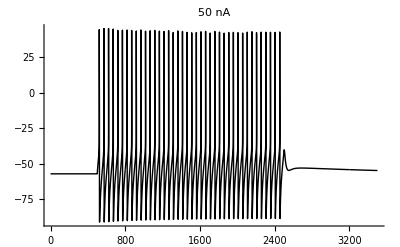

```mathematica
ListPlot[vShow[[1]],PlotStyle->Black,PlotLabel->ToString[pulseSize[[1]]]<>" nA",AxesOrigin->{0,-95}]
```

```mathematica
ListPlot[vShow[[3;;]],PlotStyle->Black,PlotLabel->StringDrop[StringJoin[Table[ToString[i]<>", ",{i,Sort[pulseSize[[2;;]]]}]],-2]<>" nA",AxesOrigin->{0,-105},PlotRange->{{0,All},{-105,All}}]
```

-Graphics-

### Single IPSP

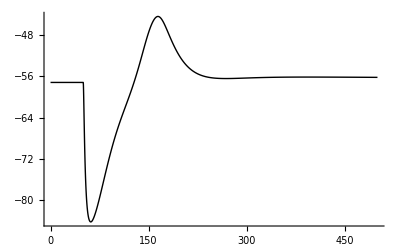

```mathematica
tStim=50;
Clear[gGaba]
gGaba[t_]:=gUnitaryGaba gabaPsc[t,tStim];
tf=500;
showTimes=Table[t,{t,0,tf,0.1}];

diffEq={
v'[t]==vDot[v[t],0,0,gGaba[t],hNa[t],mKdr[t],mA[t],hA[t],mD[t],hD[t],mK2[t],hK2[t],mH[t],mT[t],hT[t]],
hNa'[t]==xDot[hNa[t],inactInfNa[v[t]],QiNa inactTauNa[v[t]]],
mKdr'[t]==xDot[mKdr[t],actInfKdr[v[t]],QaKdr actTauKdr[v[t]]],
mA'[t]==xDot[mA[t],actInfA[v[t]],QaA actTauA[v[t]]],
hA'[t]==xDot[hA[t],inactInfA[v[t]],QiA inactTauA[v[t]]],
mD'[t]==xDot[mD[t],actInfD[v[t]],QaD actTauD[v[t]]],
hD'[t]==xDot[hD[t],inactInfD[v[t]],QiD inactTauD[v[t]]],
mK2'[t]==xDot[mK2[t],actInfK2[v[t]],QaK2 actTauK2[v[t]]],
hK2'[t]==xDot[hK2[t],inactInfK2[v[t]],QiK2 inactTauK2[v[t]]],
mH'[t]==xDot[mH[t],actInfH[v[t]],QaH actTauH[v[t]]],
mT'[t]==xDot[mT[t],actInfT[v[t]],QaT actTauT[v[t]]],
hT'[t]==xDot[hT[t],inactInfT[v[t]],QiT inactTauT[v[t]]]
};
eqn=Join[diffEq,initCond];
s=NDSolve[eqn,{v,hNa,mKdr,mA,hA,mD,hD,mK2,hK2,mH,mT,hT},{t,0,tf},MaxSteps->Infinity];
vShow=Transpose[{showTimes,Evaluate[v[#]/.s][[1]]&/@showTimes}];
ListPlot[vShow,PlotStyle->Black]
```

## DLM at 30°C

```mathematica
SetTemperature[30,True]
```

resting potential: -56.4 mV

IPSC properties at 30 deg:
0.5 ms rise tau, 6.9 ms decay tau
14.7 nS peak unitary conductance

### Train of IPSPs

```mathematica
(* specify train parameters *)
stimInterval=10;
trainStart=100;
trainDur=500;
postTrainTime=200;
```

#### Construct GABA conductance waveform

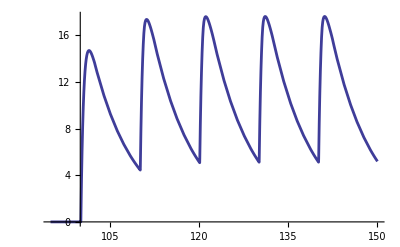

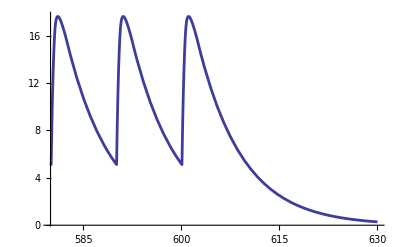

```mathematica
dt=0.1;
rise=(1-Exp[-(#)/tauRise])&/@Table[t,{t,dt,5tauRise,dt}];
rise=Rest[rise]-Most[rise];
riseBuffer=rise;
time=0;
iSyn=0;
iTraj={};
While[time<tauRise+tauDecay,
ptr=Mod[Round[time/dt]+1,Length[rise],1];
iSyn+=riseBuffer[[ptr]];
riseBuffer[[ptr]]=0;
iSyn-=(iSyn/tauDecay)dt;
AppendTo[iTraj,iSyn];
time+=dt
];
norm=1/Max[iTraj];
rise=norm rise;
risePts=Length[rise];
iSyn=0;
iSynTraj={};
riseBuffer=0 rise;
xSpikes=Table[t,{t,trainStart,trainStart+trainDur,stimInterval}];
xSpikes=dt (xSpikes/dt);
tf=trainStart+trainDur+postTrainTime;
Do[
AppendTo[iSynTraj,{t,iSyn}];
ptr=Mod[Round[t/dt]+1,risePts,1];
iSyn+=SaturateDeriv[iSyn,gUnitaryGaba,gMaxGaba]riseBuffer[[ptr]];
iSyn-=(iSyn/tauDecay)dt;
riseBuffer[[ptr]]=0;
If[MemberQ[xSpikes,t],
loc=Mod[Table[i,{i,ptr+1,ptr+risePts}],risePts,1];
riseBuffer[[loc]]+=gUnitaryGaba rise
],
{t,0,tf,dt}];
gGaba=Interpolation[iSynTraj,InterpolationOrder->1];
Plot[gGaba[t],{t,trainStart-5,trainStart+50}]
Plot[gGaba[t],{t,trainStart+trainDur-2stimInterval,trainStart+trainDur+3 stimInterval}]
```

#### Simulate Response

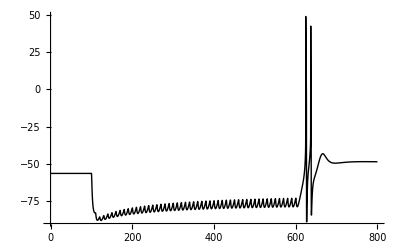

```mathematica
showTimes=Table[t,{t,0,tf,0.1}];

diffEq={
v'[t]==vDot[v[t],0,0,gGaba[t],hNa[t],mKdr[t],mA[t],hA[t],mD[t],hD[t],mK2[t],hK2[t],mH[t],mT[t],hT[t]],
hNa'[t]==xDot[hNa[t],inactInfNa[v[t]],QiNa inactTauNa[v[t]]],
mKdr'[t]==xDot[mKdr[t],actInfKdr[v[t]],QaKdr actTauKdr[v[t]]],
mA'[t]==xDot[mA[t],actInfA[v[t]],QaA actTauA[v[t]]],
hA'[t]==xDot[hA[t],inactInfA[v[t]],QiA inactTauA[v[t]]],
mD'[t]==xDot[mD[t],actInfD[v[t]],QaD actTauD[v[t]]],
hD'[t]==xDot[hD[t],inactInfD[v[t]],QiD inactTauD[v[t]]],
mK2'[t]==xDot[mK2[t],actInfK2[v[t]],QaK2 actTauK2[v[t]]],
hK2'[t]==xDot[hK2[t],inactInfK2[v[t]],QiK2 inactTauK2[v[t]]],
mH'[t]==xDot[mH[t],actInfH[v[t]],QaH actTauH[v[t]]],
mT'[t]==xDot[mT[t],actInfT[v[t]],QaT actTauT[v[t]]],
hT'[t]==xDot[hT[t],inactInfT[v[t]],QiT inactTauT[v[t]]]
};
eqn=Join[diffEq,initCond];
s=NDSolve[eqn,{v,hNa,mKdr,mA,hA,mD,hD,mK2,hK2,mH,mT,hT},{t,0,tf},MaxSteps->Infinity];
vShow=Transpose[{showTimes,Evaluate[v[#]/.s][[1]]&/@showTimes}];
ListPlot[vShow,PlotStyle->Black,AxesOrigin->{0,-90}]
```

```mathematica
Print["burst latency: ",FindSpikes[vShow][[1,1]]-xSpikes[[-1]]," ms"];
```

burst latency: 24.5 ms

## DLM at 41°C

```mathematica
SetTemperature[41,True]
```

resting potential: -54.4 mV

IPSC properties at 41 deg:
0.2 ms rise tau, 3.1 ms decay tau
23. nS peak unitary conductance

### Adjust Leak Conductance to Make Model Conform to Recorded In Vivo Behavior

```mathematica
(* separate general leak conductance into Na and K components *)
gLeakNa=gLeak(eLeak-eK)/(eNa-eK)
gLeakK=gLeak(eLeak-eNa)/(eK-eNa)
```

0.4

1.1

LeakCalculator gives the values for gLeak and eLeak corresponding to desired values of K^+ and Na^+ leak conductances.

```mathematica
LeakCalculator[gK_,gNa_]:={gK+gNa,(gK eK+gNa eNa)/(gK+gNa)}
```

```mathematica
(* increase K leak *)
{gLeak,eLeak}=LeakCalculator[2.6,gLeakNa]
```

{3.,-80.}

### Rebound

#### Define Inputs

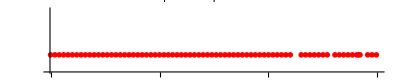

```mathematica
trainDur=600;
baseIsi=8;
pauseIsi1=20;
pauseIsi2=14;
burstIsi=3;
pauseStart1=440;
pauseStart2=510;
burstStart=565;
burstIsiN=2;
xSpikes=Range[0,pauseStart1,baseIsi];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi1];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,pauseStart2,baseIsi]];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi2];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,burstStart,baseIsi]];
xSpikes=Join[xSpikes,Table[xSpikes[[-1]]+i burstIsi,{i,burstIsiN}]];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi2];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,trainDur,baseIsi]];
pallSpikes=Transpose[{xSpikes,Table[0.5,{i,xSpikes}]}];
len=0.3;
marker=Graphics[{Red,Line[{{0,-0.5len},{0,0.5len}}]}];
ListPlot[pallSpikes,PlotMarkers->marker,Joined->False,PlotRange->{{0,trainDur},{-0.1,2.1}},PlotStyle->Red,AspectRatio->0.2,AxesOrigin->{-1,-0.1},Ticks->{{0,200,400,600},None},PlotLabel->"pallidal spike train"]
```

```mathematica
gGlut[t_]:=0;
```

#### Simulate Thalamic Response

```mathematica
blockDur=trainDur;
Print["simulating block ",Dynamic[block]," of ",Dynamic[nBlocks]]
Print["elapsed time: ",Dynamic[eTime]," min"]
```

simulating block  of

elapsed time:  min

```mathematica
nBlocks=Floor[trainDur/blockDur];
startCond=initCond;
remainder={};
dlmSpikes={};
dtRec=0.1;
t1=SessionTime[];
dtSyn=0.05;
spk=Append[Round[xSpikes,dtSyn],trainDur+1];
rise=(1-Exp[-(#)/tauRise])&/@Table[t,{t,dtSyn,5tauRise,dtSyn}];
rise=Rest[rise]-Most[rise];
riseBuffer=rise;
time=0;
iSyn=0;
iTraj={};
While[time<tauRise+tauDecay,
ptr=Mod[Round[time/dtSyn]+1,Length[rise],1];
iSyn+=riseBuffer[[ptr]];
riseBuffer[[ptr]]=0;
iSyn-=(iSyn/tauDecay)dtSyn;
AppendTo[iTraj,iSyn];
time+=dtSyn
];
norm=1/Max[iTraj];
rise=norm rise;
risePts=Length[rise];
{oldSyn,oldBuffer}={0,0 rise};

Do[
block=n;
eTime=(SessionTime[]-t1)/60;

(* compute gGaba for this block *)
gSyn=oldSyn;
riseBuffer=oldBuffer;
gSynTraj={};
Do[
AppendTo[gSynTraj,{t,gSyn}];
ptr=Mod[Round[t/dtSyn]+1,risePts,1];
oldSyn=gSyn;
oldBuffer=riseBuffer;
gSyn+=SaturateDeriv[gSyn,gUnitaryGaba,gMaxGaba]riseBuffer[[ptr]];
gSyn-=(gSyn/tauDecay)dtSyn;
riseBuffer[[ptr]]=0;
If[Abs[t-spk[[1]]]<dtSyn,
loc=Mod[Table[i,{i,ptr+1,ptr+risePts}],risePts,1];
riseBuffer[[loc]]+=gUnitaryGaba rise;
spk=Rest[spk]
],
{t,(n-1)blockDur,n blockDur,dtSyn}];
gGaba=Interpolation[gSynTraj,InterpolationOrder->1];

(* simulate block *)
diffEq={
v'[t]==vDot[v[t],0,gGlut[t],gGaba[t],hNa[t],mKdr[t],mA[t],hA[t],mD[t],hD[t],mK2[t],hK2[t],mH[t],mT[t],hT[t]],
hNa'[t]==xDot[hNa[t],inactInfNa[v[t]],QiNa inactTauNa[v[t]]],
mKdr'[t]==xDot[mKdr[t],actInfKdr[v[t]],QaKdr actTauKdr[v[t]]],
mA'[t]==xDot[mA[t],actInfA[v[t]],QaA actTauA[v[t]]],
hA'[t]==xDot[hA[t],inactInfA[v[t]],QiA inactTauA[v[t]]],
mD'[t]==xDot[mD[t],actInfD[v[t]],QaD actTauD[v[t]]],
hD'[t]==xDot[hD[t],inactInfD[v[t]],QiD inactTauD[v[t]]],
mK2'[t]==xDot[mK2[t],actInfK2[v[t]],QaK2 actTauK2[v[t]]],
hK2'[t]==xDot[hK2[t],inactInfK2[v[t]],QiK2 inactTauK2[v[t]]],
mH'[t]==xDot[mH[t],actInfH[v[t]],QaH actTauH[v[t]]],
mT'[t]==xDot[mT[t],actInfT[v[t]],QaT actTauT[v[t]]],
hT'[t]==xDot[hT[t],inactInfT[v[t]],QiT inactTauT[v[t]]]
};
eqn=Join[diffEq,startCond];
s=NDSolve[eqn,{v,hNa,mKdr,mA,hA,mD,hD,mK2,hK2,mH,mT,hT},{t,(n-1)blockDur,n blockDur},MaxSteps->Infinity];

times=Table[t,{t,(n-1)blockDur,n blockDur,dtRec}];
vTraj=Transpose[{times,Evaluate[v[#]/.s][[1]]&/@times}];
{tmpSpk,remainder}=FindSpikes[Join[remainder,vTraj]];
dlmSpikes=Join[dlmSpikes,tmpSpk];

(* set initial conditions for next block *)
startCond={
v[n blockDur]==Evaluate[v[n blockDur]/.s][[1]],
hNa[n blockDur]==Evaluate[hNa[n blockDur]/.s][[1]],
mKdr[n blockDur]==Evaluate[mKdr[n blockDur]/.s][[1]],
mD[n blockDur]==Evaluate[mD[n blockDur]/.s][[1]],
hD[n blockDur]==Evaluate[hD[n blockDur]/.s][[1]],
mA[n blockDur]==Evaluate[mA[n blockDur]/.s][[1]],
hA[n blockDur]==Evaluate[hA[n blockDur]/.s][[1]],
mK2[n blockDur]==Evaluate[mK2[n blockDur]/.s][[1]],
hK2[n blockDur]==Evaluate[hK2[n blockDur]/.s][[1]],
mH[n blockDur]==Evaluate[mH[n blockDur]/.s][[1]],
mT[n blockDur]==Evaluate[mT[n blockDur]/.s][[1]],
hT[n blockDur]==Evaluate[hT[n blockDur]/.s][[1]]
},
{n,nBlocks}]
```

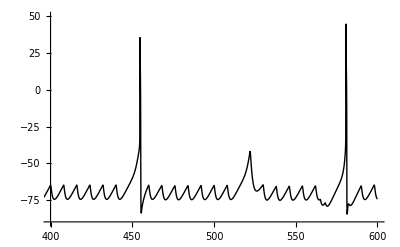

```mathematica
times=Table[t,{t,225,trainDur,0.1}];
vTraj=Transpose[{times,Evaluate[v[#]/.s][[1]]&/@times}];
ListPlot[vTraj,PlotStyle->Black,PlotRange->{{400,trainDur},{-90,50}},AxesOrigin->{400,-90}]
```

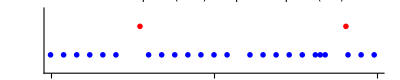

```mathematica
thalSpikes=Transpose[{dlmSpikes,Table[1.5,{i,dlmSpikes}]}];
len=0.3;
marker={Graphics[{Red,Line[{{0,-0.5len},{0,0.5len}}]}],Graphics[{Blue,Line[{{0,-0.5len},{0,0.5len}}]}]};
ListPlot[{pallSpikes,thalSpikes},PlotMarkers->marker,Joined->False,PlotRange->{{400,trainDur},{-0.1,2.1}},PlotStyle->{Blue,Red},AspectRatio->0.2,AxesOrigin->{-1,-0.1},Ticks->{{400,500,600},None},PlotLabel->"thalamic spikes (blue) and pallidal spikes (red)"]
```

### Gating/Disinhibition

#### Define Inputs

```mathematica
trainDur=600;
baseIsi=8;
pauseIsi1=20;
pauseIsi2=14;
burstIsi=3;
pauseStart1=440;
pauseStart2=510;
burstStart=565;
burstIsiN=2;
xSpikes=Range[0,pauseStart1,baseIsi];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi1];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,pauseStart2,baseIsi]];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi2];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,burstStart,baseIsi]];
xSpikes=Join[xSpikes,Table[xSpikes[[-1]]+i burstIsi,{i,burstIsiN}]];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi2];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,trainDur,baseIsi]];
pallSpikes=Transpose[{xSpikes,Table[0.5,{i,xSpikes}]}];
len=0.3;
marker=Graphics[{Red,Line[{{0,-0.5len},{0,0.5len}}]}];
ListPlot[pallSpikes,PlotMarkers->marker,Joined->False,PlotRange->{{0,trainDur},{-0.1,2.1}},PlotStyle->Red,AspectRatio->0.2,AxesOrigin->{-1,-0.1},Ticks->{{0,200,400,600},None},PlotLabel->"pallidal spike train"]
```

-Graphics-

```mathematica
gGlut[t_]:=10;
```

#### Simulate Thalamic Response

```mathematica
blockDur=trainDur;
Print["simulating block ",Dynamic[block]," of ",Dynamic[nBlocks]]
Print["elapsed time: ",Dynamic[eTime]," min"]
```

simulating block  of

elapsed time:  min

```mathematica
nBlocks=Floor[trainDur/blockDur];
startCond=initCond;
remainder={};
dlmSpikes={};
dtRec=0.1;
t1=SessionTime[];
dtSyn=0.05;
spk=Append[Round[xSpikes,dtSyn],trainDur+1];
rise=(1-Exp[-(#)/tauRise])&/@Table[t,{t,dtSyn,5tauRise,dtSyn}];
rise=Rest[rise]-Most[rise];
riseBuffer=rise;
time=0;
iSyn=0;
iTraj={};
While[time<tauRise+tauDecay,
ptr=Mod[Round[time/dtSyn]+1,Length[rise],1];
iSyn+=riseBuffer[[ptr]];
riseBuffer[[ptr]]=0;
iSyn-=(iSyn/tauDecay)dtSyn;
AppendTo[iTraj,iSyn];
time+=dtSyn
];
norm=1/Max[iTraj];
rise=norm rise;
risePts=Length[rise];
{oldSyn,oldBuffer}={0,0 rise};

Do[
block=n;
eTime=(SessionTime[]-t1)/60;

(* compute gGaba for this block *)
gSyn=oldSyn;
riseBuffer=oldBuffer;
gSynTraj={};
Do[
AppendTo[gSynTraj,{t,gSyn}];
ptr=Mod[Round[t/dtSyn]+1,risePts,1];
oldSyn=gSyn;
oldBuffer=riseBuffer;
gSyn+=SaturateDeriv[gSyn,gUnitaryGaba,gMaxGaba]riseBuffer[[ptr]];
gSyn-=(gSyn/tauDecay)dtSyn;
riseBuffer[[ptr]]=0;
If[Abs[t-spk[[1]]]<dtSyn,
loc=Mod[Table[i,{i,ptr+1,ptr+risePts}],risePts,1];
riseBuffer[[loc]]+=gUnitaryGaba rise;
spk=Rest[spk]
],
{t,(n-1)blockDur,n blockDur,dtSyn}];
gGaba=Interpolation[gSynTraj,InterpolationOrder->1];

(* simulate block *)
diffEq={
v'[t]==vDot[v[t],0,gGlut[t],gGaba[t],hNa[t],mKdr[t],mA[t],hA[t],mD[t],hD[t],mK2[t],hK2[t],mH[t],mT[t],hT[t]],
hNa'[t]==xDot[hNa[t],inactInfNa[v[t]],QiNa inactTauNa[v[t]]],
mKdr'[t]==xDot[mKdr[t],actInfKdr[v[t]],QaKdr actTauKdr[v[t]]],
mA'[t]==xDot[mA[t],actInfA[v[t]],QaA actTauA[v[t]]],
hA'[t]==xDot[hA[t],inactInfA[v[t]],QiA inactTauA[v[t]]],
mD'[t]==xDot[mD[t],actInfD[v[t]],QaD actTauD[v[t]]],
hD'[t]==xDot[hD[t],inactInfD[v[t]],QiD inactTauD[v[t]]],
mK2'[t]==xDot[mK2[t],actInfK2[v[t]],QaK2 actTauK2[v[t]]],
hK2'[t]==xDot[hK2[t],inactInfK2[v[t]],QiK2 inactTauK2[v[t]]],
mH'[t]==xDot[mH[t],actInfH[v[t]],QaH actTauH[v[t]]],
mT'[t]==xDot[mT[t],actInfT[v[t]],QaT actTauT[v[t]]],
hT'[t]==xDot[hT[t],inactInfT[v[t]],QiT inactTauT[v[t]]]
};
eqn=Join[diffEq,startCond];
s=NDSolve[eqn,{v,hNa,mKdr,mA,hA,mD,hD,mK2,hK2,mH,mT,hT},{t,(n-1)blockDur,n blockDur},MaxSteps->Infinity];

times=Table[t,{t,(n-1)blockDur,n blockDur,dtRec}];
vTraj=Transpose[{times,Evaluate[v[#]/.s][[1]]&/@times}];
{tmpSpk,remainder}=FindSpikes[Join[remainder,vTraj]];
dlmSpikes=Join[dlmSpikes,tmpSpk];

(* set initial conditions for next block *)
startCond={
v[n blockDur]==Evaluate[v[n blockDur]/.s][[1]],
hNa[n blockDur]==Evaluate[hNa[n blockDur]/.s][[1]],
mKdr[n blockDur]==Evaluate[mKdr[n blockDur]/.s][[1]],
mD[n blockDur]==Evaluate[mD[n blockDur]/.s][[1]],
hD[n blockDur]==Evaluate[hD[n blockDur]/.s][[1]],
mA[n blockDur]==Evaluate[mA[n blockDur]/.s][[1]],
hA[n blockDur]==Evaluate[hA[n blockDur]/.s][[1]],
mK2[n blockDur]==Evaluate[mK2[n blockDur]/.s][[1]],
hK2[n blockDur]==Evaluate[hK2[n blockDur]/.s][[1]],
mH[n blockDur]==Evaluate[mH[n blockDur]/.s][[1]],
mT[n blockDur]==Evaluate[mT[n blockDur]/.s][[1]],
hT[n blockDur]==Evaluate[hT[n blockDur]/.s][[1]]
},
{n,nBlocks}]
```

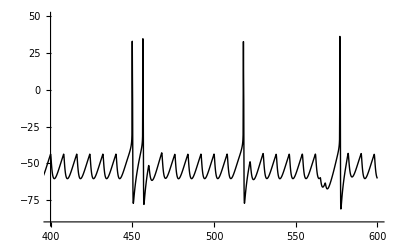

```mathematica
times=Table[t,{t,225,trainDur,0.1}];
vTraj=Transpose[{times,Evaluate[v[#]/.s][[1]]&/@times}];
ListPlot[vTraj,PlotStyle->Black,PlotRange->{{400,trainDur},{-90,50}},AxesOrigin->{400,-90}]
```

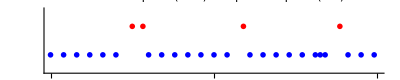

```mathematica
thalSpikes=Transpose[{dlmSpikes,Table[1.5,{i,dlmSpikes}]}];
len=0.3;
marker={Graphics[{Red,Line[{{0,-0.5len},{0,0.5len}}]}],Graphics[{Blue,Line[{{0,-0.5len},{0,0.5len}}]}]};
ListPlot[{pallSpikes,thalSpikes},PlotMarkers->marker,Joined->False,PlotRange->{{400,trainDur},{-0.1,2.1}},PlotStyle->{Blue,Red},AspectRatio->0.2,AxesOrigin->{-1,-0.1},Ticks->{{400,500,600},None},PlotLabel->"thalamic spikes (blue) and pallidal spikes (red)"]
```

### High Frequency Entrainment

#### Define Inputs

```mathematica
trainDur=600;
baseIsi=8;
pauseIsi1=20;
pauseIsi2=14;
burstIsi=3;
pauseStart1=440;
pauseStart2=510;
burstStart=565;
burstIsiN=2;
xSpikes=Range[0,pauseStart1,baseIsi];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi1];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,pauseStart2,baseIsi]];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi2];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,burstStart,baseIsi]];
xSpikes=Join[xSpikes,Table[xSpikes[[-1]]+i burstIsi,{i,burstIsiN}]];
AppendTo[xSpikes,xSpikes[[-1]]+pauseIsi2];
xSpikes=Join[xSpikes,Range[xSpikes[[-1]]+baseIsi,trainDur,baseIsi]];
pallSpikes=Transpose[{xSpikes,Table[0.5,{i,xSpikes}]}];
len=0.3;
marker=Graphics[{Red,Line[{{0,-0.5len},{0,0.5len}}]}];
ListPlot[pallSpikes,PlotMarkers->marker,Joined->False,PlotRange->{{0,trainDur},{-0.1,2.1}},PlotStyle->Red,AspectRatio->0.2,AxesOrigin->{-1,-0.1},Ticks->{{0,200,400,600},None},PlotLabel->"pallidal spike train"]
```

-Graphics-

```mathematica
gGlut[t_]:=20;
```

#### Simulate Thalamic Response

```mathematica
blockDur=trainDur;
Print["simulating block ",Dynamic[block]," of ",Dynamic[nBlocks]]
Print["elapsed time: ",Dynamic[eTime]," min"]
```

simulating block  of

elapsed time:  min

```mathematica
nBlocks=Floor[trainDur/blockDur];
startCond=initCond;
remainder={};
dlmSpikes={};
dtRec=0.1;
t1=SessionTime[];
dtSyn=0.05;
spk=Append[Round[xSpikes,dtSyn],trainDur+1];
rise=(1-Exp[-(#)/tauRise])&/@Table[t,{t,dtSyn,5tauRise,dtSyn}];
rise=Rest[rise]-Most[rise];
riseBuffer=rise;
time=0;
iSyn=0;
iTraj={};
While[time<tauRise+tauDecay,
ptr=Mod[Round[time/dtSyn]+1,Length[rise],1];
iSyn+=riseBuffer[[ptr]];
riseBuffer[[ptr]]=0;
iSyn-=(iSyn/tauDecay)dtSyn;
AppendTo[iTraj,iSyn];
time+=dtSyn
];
norm=1/Max[iTraj];
rise=norm rise;
risePts=Length[rise];
{oldSyn,oldBuffer}={0,0 rise};

Do[
block=n;
eTime=(SessionTime[]-t1)/60;

(* compute gGaba for this block *)
gSyn=oldSyn;
riseBuffer=oldBuffer;
gSynTraj={};
Do[
AppendTo[gSynTraj,{t,gSyn}];
ptr=Mod[Round[t/dtSyn]+1,risePts,1];
oldSyn=gSyn;
oldBuffer=riseBuffer;
gSyn+=SaturateDeriv[gSyn,gUnitaryGaba,gMaxGaba]riseBuffer[[ptr]];
gSyn-=(gSyn/tauDecay)dtSyn;
riseBuffer[[ptr]]=0;
If[Abs[t-spk[[1]]]<dtSyn,
loc=Mod[Table[i,{i,ptr+1,ptr+risePts}],risePts,1];
riseBuffer[[loc]]+=gUnitaryGaba rise;
spk=Rest[spk]
],
{t,(n-1)blockDur,n blockDur,dtSyn}];
gGaba=Interpolation[gSynTraj,InterpolationOrder->1];

(* simulate block *)
diffEq={
v'[t]==vDot[v[t],0,gGlut[t],gGaba[t],hNa[t],mKdr[t],mA[t],hA[t],mD[t],hD[t],mK2[t],hK2[t],mH[t],mT[t],hT[t]],
hNa'[t]==xDot[hNa[t],inactInfNa[v[t]],QiNa inactTauNa[v[t]]],
mKdr'[t]==xDot[mKdr[t],actInfKdr[v[t]],QaKdr actTauKdr[v[t]]],
mA'[t]==xDot[mA[t],actInfA[v[t]],QaA actTauA[v[t]]],
hA'[t]==xDot[hA[t],inactInfA[v[t]],QiA inactTauA[v[t]]],
mD'[t]==xDot[mD[t],actInfD[v[t]],QaD actTauD[v[t]]],
hD'[t]==xDot[hD[t],inactInfD[v[t]],QiD inactTauD[v[t]]],
mK2'[t]==xDot[mK2[t],actInfK2[v[t]],QaK2 actTauK2[v[t]]],
hK2'[t]==xDot[hK2[t],inactInfK2[v[t]],QiK2 inactTauK2[v[t]]],
mH'[t]==xDot[mH[t],actInfH[v[t]],QaH actTauH[v[t]]],
mT'[t]==xDot[mT[t],actInfT[v[t]],QaT actTauT[v[t]]],
hT'[t]==xDot[hT[t],inactInfT[v[t]],QiT inactTauT[v[t]]]
};
eqn=Join[diffEq,startCond];
s=NDSolve[eqn,{v,hNa,mKdr,mA,hA,mD,hD,mK2,hK2,mH,mT,hT},{t,(n-1)blockDur,n blockDur},MaxSteps->Infinity];

times=Table[t,{t,(n-1)blockDur,n blockDur,dtRec}];
vTraj=Transpose[{times,Evaluate[v[#]/.s][[1]]&/@times}];
{tmpSpk,remainder}=FindSpikes[Join[remainder,vTraj]];
dlmSpikes=Join[dlmSpikes,tmpSpk];

(* set initial conditions for next block *)
startCond={
v[n blockDur]==Evaluate[v[n blockDur]/.s][[1]],
hNa[n blockDur]==Evaluate[hNa[n blockDur]/.s][[1]],
mKdr[n blockDur]==Evaluate[mKdr[n blockDur]/.s][[1]],
mD[n blockDur]==Evaluate[mD[n blockDur]/.s][[1]],
hD[n blockDur]==Evaluate[hD[n blockDur]/.s][[1]],
mA[n blockDur]==Evaluate[mA[n blockDur]/.s][[1]],
hA[n blockDur]==Evaluate[hA[n blockDur]/.s][[1]],
mK2[n blockDur]==Evaluate[mK2[n blockDur]/.s][[1]],
hK2[n blockDur]==Evaluate[hK2[n blockDur]/.s][[1]],
mH[n blockDur]==Evaluate[mH[n blockDur]/.s][[1]],
mT[n blockDur]==Evaluate[mT[n blockDur]/.s][[1]],
hT[n blockDur]==Evaluate[hT[n blockDur]/.s][[1]]
},
{n,nBlocks}]
```

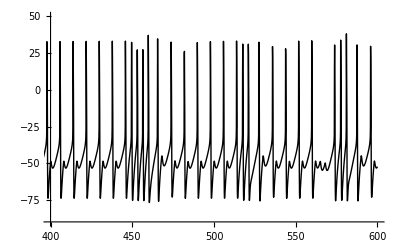

```mathematica
times=Table[t,{t,225,trainDur,0.1}];
vTraj=Transpose[{times,Evaluate[v[#]/.s][[1]]&/@times}];
ListPlot[vTraj,PlotStyle->Black,PlotRange->{{400,trainDur},{-90,50}},AxesOrigin->{400,-90}]
```

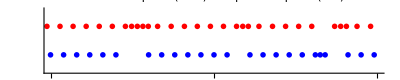

```mathematica
thalSpikes=Transpose[{dlmSpikes,Table[1.5,{i,dlmSpikes}]}];
len=0.3;
marker={Graphics[{Red,Line[{{0,-0.5len},{0,0.5len}}]}],Graphics[{Blue,Line[{{0,-0.5len},{0,0.5len}}]}]};
ListPlot[{pallSpikes,thalSpikes},PlotMarkers->marker,Joined->False,PlotRange->{{400,trainDur},{-0.1,2.1}},PlotStyle->{Blue,Red},AspectRatio->0.2,AxesOrigin->{-1,-0.1},Ticks->{{400,500,600},None},PlotLabel->"thalamic spikes (blue) and pallidal spikes (red)"]
```